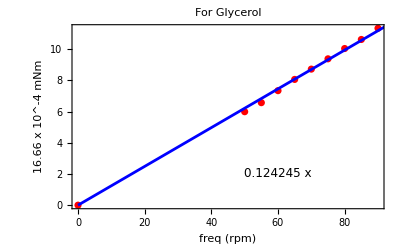

```mathematica
data={{0,0},{50,5.99},{55,6.57},{60,7.34},{65,8.06},{70,8.72},{75,9.38},{80,10.04},{85,10.62},{90,11.34}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Glycerol",Epilog->{Text[Style[eqn,12],{60,2}]}]
```

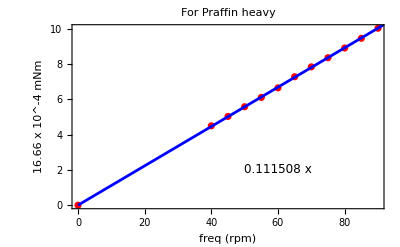

```mathematica
data={{0,0},{40,4.5},{45,5.03},{50,5.58},{55,6.11},{60,6.65},{65,7.28},{70,7.84},{75,8.36},{80,8.91},{85,9.46},{90,10.03}};
fit=Fit[data,{x},x];
eqn=ToString[fit,TraditionalForm]; (*Create equation string*)

Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,0,100},PlotStyle->Blue],Frame->True,FrameLabel->{"freq (rpm)","16.66 x 10^-4 mNm"},PlotLabel->"For Praffin heavy",Epilog->{Text[Style[eqn,12],{60,2}]}]
```

```mathematica
ClearAll["Global"]
```

ListPlot::lpn: Pattern[(#1&)[data],_seaback] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[data_seaback,PlotStyle→color],,Frame→True,FrameLabel→{Temperature (°C),Voltage (mV)},PlotLabel→Seebeck Coefficient,Epilog→{Text[0.0506786 x-0.888214,{140,6}]}].

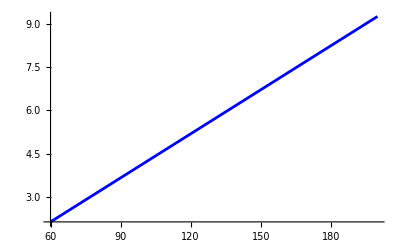
Show[ListPlot[data_seaback,PlotStyle→RGBColor[1, 0, 0]],-Graphics-,Frame→True,FrameLabel→{Temperature (°C),Voltage (mV)},PlotLabel→Seebeck Coefficient,Epilog→{Text[0.0506786 x-0.888214,{140,6}]}]

```mathematica
data={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};

(*Proper linear fit with intercept*)
fit=Fit[data,{1,x},x];

Show[ListPlot[data_seaback,PlotStyle->Red],Plot[fit,{x,60,200},PlotStyle->Blue],Frame->True,FrameLabel->{"Temperature (°C)","Voltage (mV)"},PlotLabel->"Seebeck Coefficient",Epilog->{Text[Style[ToString[fit,TraditionalForm],12],{140,6}]}]
```

best equation Get line of the^2 (-0.888214+0.0506786 x)

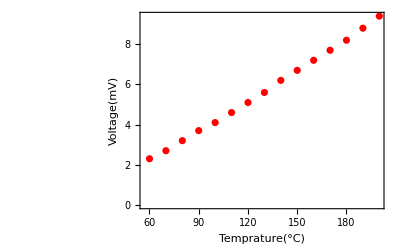

```mathematica
data2={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};
fit2=LinearModelFit[data2,x,x];
eqn2=fit2["BestFit"];(Get the equation of the best fit line)
Show[ListPlot[data2,PlotStyle->Red],Plot[fit2[x],{x,0,20},PlotStyle->Blue],Frame->True,FrameLabel->{"Temprature(°C)","Voltage(mV)"},Epilog->Inset[Style[eqn2,12],{6,-0.5}]]
```

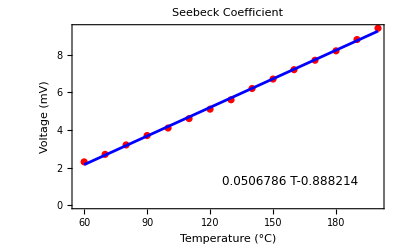

```mathematica
data2={{200,9.4},{190,8.8},{180,8.2},{170,7.7},{160,7.2},{150,6.7},{140,6.2},{130,5.6},{120,5.1},{110,4.6},{100,4.1},{90,3.7},{80,3.2},{70,2.7},{60,2.3}};
fit2=LinearModelFit[data2,{T},T];  (*Replace x with T*)
eqn2=fit2["BestFit"];

Show[ListPlot[data2,PlotStyle->Red],Plot[fit2[T],{T,60,200},PlotStyle->Blue],Frame->True,FrameLabel->{"Temperature (°C)","Voltage (mV)"},PlotLabel->"Seebeck Coefficient",Epilog->Inset[Style[eqn2,12],Scaled[{0.7,0.15}]]]
```